# (2) Scalar perturbations

## Reference: E. Berti’s Black Hole Perturbation Theory Notes (ICTS) [https://www.icts.res.in/event/page/3071] Equation numbers cited throughout this document follow the numbering convention used in these notes to facilitate cross-referencing.

## (0) Set-up

```mathematica
SetDirectory["C:\Program Files\Wolfram Research\Mathematica\12.1\AddOns\Applications\xAct_1.2.0"];
```

```mathematica
<<xAct`xPert`(*perturbation theory*)
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
<<xAct`xCoba`(*tensor component calculations*)
```

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<MaTeX` ;(*LaTeX integration in text and output cells*)
```

```mathematica
<<xAct`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
SetOptions[MaTeX,FontSize->14];
```

```mathematica
mt = MaTeX;
```

Syntax to generate MaTeX formatted numbered equations:  “<expression>  \qquad   <equation_number> “ // mt
Execute the above in an input cell, and then paste result in a text cell.

```mathematica
$DefInfoQ=False;  (*turns off optional xAct messages*)
```

## (I) Definitions

```mathematica
DefManifold[M,4,IndexRange[a,f]]
```

```mathematica
DefMetric[-1,g[-a,-b],CD]
```

```mathematica
DefChart[B,M,{0,1,2,3},{t[],r[],θ[],ϕ[]}]
```

Define the scalar field, ϕ

```mathematica
DefTensor[phi[],M, PrintAs->"ϕ"];
```

Define the mass of the scalar field, μ

```mathematica
DefConstantSymbol[mphi, PrintAs->"μ"]
```

Define metric perturbation, h_μν

```mathematica
DefMetricPerturbation[g,h,ϵ]
```

Define scalar field perturbation, δϕ

```mathematica
DefTensorPerturbation[delphi[LI[1]],phi[],{M},PrintAs->"δϕ"]
```

Notational clean-up

```mathematica
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[K]^="F";
PrintAs[EinsteinCD]^="G";
$CovDFormat="Prefix";
PrintAs[Detg]^= "g";
```

## (III) The energy-momentum tensor and the Klein-Gordon equation

Classical scalar field (linear) theory Lagrangian:

```mathematica
L=Sqrt[-Detg[]]((-1/2)CD[-a][phi[]]*CD[a][phi[]] - (1/2)mphi^2 * phi[]^2)//SeparateMetric[g]
```

√-g (-1/2 μ^2 ϕ^2-1/2 g | a | b
  |   (▽_a ϕ) (▽_b ϕ))

First order variation in L

```mathematica
Lpert=L//Perturbation
```

-(△[g] (-1/2 μ^2 ϕ^2-1/2 g | a | b
  |   (▽_a ϕ) (▽_b ϕ)))/(2 √-g)+√-g (-μ^2 δϕ | 1
  ϕ+1/2 (-g | a | b
  |   (▽_a ϕ) (▽_b δϕ | 1
 )-g | a | b
  |   (▽_a δϕ | 1
 ) (▽_b ϕ)-△[g | a | b
  |  ] (▽_a ϕ) (▽_b ϕ)))

Variation in L expanded out in terms of the variation in our fundamental dynamical variables i.e. the metric, and the vector field

```mathematica
LpertExpanded = Lpert//ExpandPerturbation//Expand
```

-μ^2 δϕ | 1
  √-g ϕ-1/4 μ^2 √-g h | 1 |   | a
  | a |   ϕ^2-1/2 √-g g | a | b
  |   (▽_a ϕ) (▽_b δϕ | 1
 )-1/2 √-g g | a | b
  |   (▽_a δϕ | 1
 ) (▽_b ϕ)+1/2 √-g h | 1 | a | b
  |   |   (▽_a ϕ) (▽_b ϕ)-1/4 √-g g | a | b
  |   h | 1 |   | c
  | c |   (▽_a ϕ) (▽_b ϕ)

#### Energy-momentum tensor

```mathematica
tempMet1 =LpertExpanded//VarD[h[LI[1],a,b],CD]
```

-1/4 μ^2 δ |   | 1
1 |   √-g g |   |  
a | b ϕ^2+1/2 δ |   | 1
1 |   √-g (▽_a ϕ) (▽_b ϕ)-1/4 δ |   | 1
1 |   √-g g |   |  
a | b g | c | d
  |   (▽_c ϕ) (▽_d ϕ)

Substituting the value of the Kronecker delta component, δ |   | 1
1 |   = 1

```mathematica
tempMet2 = tempMet1/.delta[-LI[1],LI[1]]->1;
```

Since field equations are derived by imposing that the variation in action is zero, we can simplify our expression by multiplying with factor of 1/Sqrt[-Detg[]]

```mathematica
energyMomentum = (-2/Sqrt[-Detg[]])tempMet2//Expand//ToCanonical//ContractMetric
```

1/2 μ^2 g |   |  
a | b ϕ^2-(▽_a ϕ) (▽_b ϕ)+1/2 g |   |  
a | b (▽_c ϕ) (▽^c ϕ)

#### (iii) Klein-Gordon equation

```mathematica
tempScalar1 =LpertExpanded//VarD[delphi[LI[1]],CD]
```

-μ^2 δ |   | 1
1 |   √-g ϕ+δ |   | 1
1 |   √-g g | a | b
  |   (▽_b▽_a ϕ)

Substituting the value of the Kronecker delta component, δ |   | 1
1 |   = 1

```mathematica
tempScalar2= tempScalar1/.delta[-LI[1],LI[1]]->1;
```

Since field equations are derived by imposing that the variation in action is zero, we can simplify our expression by multiplying with factor of 2/Sqrt[-Detg[]]

```mathematica
tempScalar3= (1/Sqrt[-Detg[]])tempScalar2//Expand//ToCanonical//ContractMetric//ScreenDollarIndices//ToCanonical
```

-μ^2 ϕ+▽_a▽^a ϕ

Finally, obtaining the Klein-Gordon equation

```mathematica
eqnKG = tempScalar3==0
```

-μ^2 ϕ+▽_a▽^a ϕ==0

```mathematica
eqnKGfirst = eqnKG//First
```

-μ^2 ϕ+▽_a▽^a ϕ

## Scalar perturbations

```mathematica
pert1=eqnKGfirst//SeparateMetric[g]//Perturbation//ExpandPerturbation//Expand
```

-μ^2 δϕ | 1
 +g | a | b
  |   (▽_a▽_b δϕ | 1
 )-h | 1 | a | b
  |   |   (▽_a▽_b ϕ)-1/2 g | a | b
  |   (▽_a h | 1 | c |  
  |   | b) (▽_c ϕ)-1/2 g | a | b
  |   (▽_b h | 1 | c |  
  |   | a) (▽_c ϕ)+1/2 g | a | b
  |   (▽_c ϕ) (▽^c h | 1 |   |  
  | a | b)

In this example, the metric is not a dynamical field. The metric perturbations can be set to zero.

```mathematica
pert2 = pert1/.{ h[LI[1],__]->0}
```

-μ^2 δϕ | 1
 +g | a | b
  |   (▽_a▽_b δϕ | 1
 )

### Background components

Define the background metric components () - Schwarzschild:

```mathematica
DefScalarFunction[fmet, PrintAs->"f"]
```

```mathematica
bg=CTensor[{
{-fmet[r[]],0,0,0},
{0,1/(fmet[r[]]),0,0},
{0,0,r[]^2,0},
{0,0,0,r[]^2Sin[θ[]]^2}
},{-B,-B}]
```

CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]

Inverse of the background metric ():

```mathematica
invbg=Inv[bg]
```

CTensor[{{-1/f[r],0,0,0},{0,f[r],0,0},{0,0,1/r^2,0},{0,0,0,Csc[θ]^2/r^2}},{B,B},0]

Christoffel symbols () of the background metric:

```mathematica
CDbg=LC[bg]
```

CCovD[PDB,CTensor[{{{0,f'[r]/(2 f[r]),0,0},{f'[r]/(2 f[r]),0,0,0},{0,0,0,0},{0,0,0,0}},{{1/2 f[r] f'[r],0,0,0},{0,-f'[r]/(2 f[r]),0,0},{0,0,-f[r] r,0},{0,0,0,-f[r] r Sin[θ]^2}},{{0,0,0,0},{0,0,1/r,0},{0,1/r,0,0},{0,0,0,-Cos[θ] Sin[θ]}},{{0,0,0,0},{0,0,0,1/r},{0,0,0,Cot[θ]},{0,1/r,Cot[θ],0}}},{B,-B,-B},0],CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]]

```mathematica
PDbg=PD[bg]
```

PD[CTensor[{{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}},{-B,-B},0]]

Ricci tensor () of the background metric:

```mathematica
RicciCDbg=Ricci[CDbg]
```

CTensor[{{1/2 f[r] ((2 f'[r])/r+f''[r]),0,0,0},{0,-(2 f'[r]+r f''[r])/(2 f[r] r),0,0},{0,0,1-f[r]-r f'[r],0},{0,0,0,-Sin[θ]^2 (-1+f[r]+r f'[r])}},{-B,-B},0]

Einstein tensor () of the background metric:

```mathematica
EinsteinCDbg=Einstein[CDbg]
```

CTensor[{{-(f[r] (-1+f[r]+r f'[r]))/r^2,0,0,0},{0,(-1+f[r]+r f'[r])/(f[r] r^2),0,0},{0,0,1/2 r (2 f'[r]+r f''[r]),0},{0,0,0,1/2 r Sin[θ]^2 (2 f'[r]+r f''[r])}},{-B,-B},0]

Ricci scalar () of the background metric:

```mathematica
ScalarCDbg=RicciScalar[CDbg]
```

CTensor[-(-2+2 f[r]+4 r f'[r]+r^2 f''[r])/r^2,{},0]

```mathematica
$LargeComponentSize=10000 (*Allows large cTensor output *);
```

Define the spherical harmonic function, Ylm

```mathematica
DefScalarFunction[Ylm, PrintAs->"Y_lm"]
```

Define the scalar perturbation function, ψ (t ,r )

```mathematica
DefScalarFunction[psi, PrintAs->"ψ"]
```

```mathematica
componentRules= {
  g[-a_Symbol, -b_Symbol] :> bg[-a, -b],
  g[a_Symbol, b_Symbol] :> invbg[a, b],
  CD[-a_Symbol] :> CDbg[-a],
  PD[-a_Symbol] :> PDbg[-a],
  RicciCD[-a_Symbol, -b_Symbol] :> RicciCDbg[-a, -b],
  RicciScalarCD[] :> ScalarCDbg[],
  EinsteinCD[-a_Symbol, -b_Symbol] :> EinsteinCDbg[-a, -b],
delphi[LI[1]]:> (psi[t[],r[]]/r[])Ylm[θ[],ϕ[]]
  }
```

{g |   |  
a̲ | b̲:>bg[-a,-b],g | a̲ | b̲
  |  :>invbg[a,b],CD[-a_Symbol]:>CDbg[-a],PD[-a_Symbol]:>PDbg[-a],R |   |  
a̲ | b̲:>RicciCDbg[-a,-b],R:>ScalarCDbg[],G |   |  
a̲ | b̲:>EinsteinCDbg[-a,-b],δϕ | 1
 :>(ψ[t,r] Y_lm[θ,ϕ])/r}

```mathematica
pertScalar1 = pert2/.componentRules//ContractBasis//ToBasis[B]//Simplify;
```

```mathematica
coordFuncReplace = {r[]->r,t[]->t, θ[]->θ,ϕ[]->ϕ}
```

{r→r,t→t,θ→θ,ϕ→ϕ}

Define the ‘l, m’ indices of spherical harmonics,  which are constant w.r.t. spacetime coordinates

```mathematica
DefConstantSymbol[l]
DefConstantSymbol[m]
```

The associated Legendre equation (use for simplification later)

```mathematica
assocLegendre = {Csc[θ]^2*Derivative[0,2][Ylm][θ,ϕ]+Cot[θ]*Derivative[1,0][Ylm][θ,ϕ]+Derivative[2,0][Ylm][θ,ϕ]->-(l*(1+l)*Ylm[θ,ϕ]) }
```

{Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]→-l (1+l) Y_lm[θ,ϕ]}

```mathematica
pertScalar = pertScalar1/.coordFuncReplace
```

1/r^3((r^2 Y_lm[θ,ϕ] (f[r] f'[r] ψ^(0,1)[t,r]+f[r]^2 ψ^(0,2)[t,r]-ψ^(2,0)[t,r]))/f[r]+ψ[t,r] (-r Y_lm[θ,ϕ] (μ^2 r+f'[r])+Csc[θ]^2 Y_lm^(0,2)[θ,ϕ]+Cot[θ] Y_lm^(1,0)[θ,ϕ]+Y_lm^(2,0)[θ,ϕ]))

```mathematica
Eq1 = pertScalar/.assocLegendre//Simplify
```

(Y_lm[θ,ϕ] (-ψ[t,r] (l+l^2+μ^2 r^2+r f'[r])+(r^2 (f[r] f'[r] ψ^(0,1)[t,r]+f[r]^2 ψ^(0,2)[t,r]-ψ^(2,0)[t,r]))/f[r]))/r^3

```mathematica
Eq2 =Eq1*(fmet[r]/( Subscript[Y, lm][θ,ϕ] ))//Simplify
```

(f[r] (-ψ[t,r] (l+l^2+μ^2 r^2+r f'[r])+r^2 f'[r] ψ^(0,1)[t,r])+r^2 f[r]^2 ψ^(0,2)[t,r]-r^2 ψ^(2,0)[t,r])/r^3

```mathematica
DefConstantSymbol[om, PrintAs-> "ω"]
```

Assume harmonic time dependence,  e^(-i ω t)

```mathematica
harmonicTime = {Derivative[2, 0][psi][t, r] -> -om^2 psi[t, r]}
```

{ψ^(2,0)[t,r]→-ω^2 ψ[t,r]}

```mathematica
Eq3 =Eq2/.harmonicTime//Simplify//Expand
```

(ω^2 ψ[t,r])/r-(l f[r] ψ[t,r])/r^3-(l^2 f[r] ψ[t,r])/r^3-(μ^2 f[r] ψ[t,r])/r-(f[r] ψ[t,r] f'[r])/r^2+(f[r] f'[r] ψ^(0,1)[t,r])/r+(f[r]^2 ψ^(0,2)[t,r])/r

```mathematica
radialEqn =Collect[Eq3, {psi[t, r],Derivative[0, 1][psi][t, r], Derivative[0, 2][psi][t, r]}]
```

ψ[t,r] (ω^2/r-(l f[r])/r^3-(l^2 f[r])/r^3-(μ^2 f[r])/r-(f[r] f'[r])/r^2)+(f[r] f'[r] ψ^(0,1)[t,r])/r+(f[r]^2 ψ^(0,2)[t,r])/r

This is the radial scalar wave equation, corresponds to (Eq: 3.1.6)

Moving to the tortoise coordinate, r_* which is defined as:

```mathematica
DefConstantSymbol[rs, PrintAs->"r_*"]
```

Rules for the transformation of the derivatives when moving from radial to tortoise coordinate.

```mathematica
tortoise = {Derivative[0,1][psi][t,r]->(1/fmet[r]) Derivative[0,1][psi][t,rs], Derivative[0,2][psi][t,r]->(1/fmet[r]^2) Derivative[0,2][psi][t,rs]+(-1/fmet[r]^2) D[fmet[r],r]Derivative[0,1][psi][t,rs]}
```

{ψ^(0,1)[t,r]→(ψ^(0,1)[t,r_*])/f[r],ψ^(0,2)[t,r]→-(f'[r] ψ^(0,1)[t,r_*])/f[r]^2+(ψ^(0,2)[t,r_*])/f[r]^2}

```mathematica
radialEqn/.tortoise//Simplify//Expand
```

(ω^2 ψ[t,r])/r-(l f[r] ψ[t,r])/r^3-(l^2 f[r] ψ[t,r])/r^3-(μ^2 f[r] ψ[t,r])/r-(f[r] ψ[t,r] f'[r])/r^2+(ψ^(0,2)[t,r_*])/r

```mathematica
temp =% *r//Expand
```

ω^2 ψ[t,r]-μ^2 f[r] ψ[t,r]-(l f[r] ψ[t,r])/r^2-(l^2 f[r] ψ[t,r])/r^2-(f[r] ψ[t,r] f'[r])/r+ψ^(0,2)[t,r_*]

```mathematica
schrodingerEqn = Collect[temp, {psi[t, r],Derivative[0, 1][psi][t, rs], Derivative[0, 2][psi][t, rs]}]==0
```

ψ[t,r] (ω^2-μ^2 f[r]-(l f[r])/r^2-(l^2 f[r])/r^2-(f[r] f'[r])/r)+ψ^(0,2)[t,r_*]==0

#### Sketching the potential (in terms of radial coordinate)

```mathematica
V0= -Coefficient[temp, ψ[t,r]]+om^2
```

μ^2 f[r]+(l f[r])/r^2+(l^2 f[r])/r^2+(f[r] f'[r])/r

Take BH mass, M = 1.

```mathematica
plotRules = {l->2, fmet[r]->1-2/r, Derivative[1][fmet][r]->2/r^2}
```

{l→2,f[r]→1-2/r,f'[r]→2/r^2}

```mathematica
Vtemp = V0/.plotRules//Simplify
```

((-2+r) (2+6 r+μ^2 r^3))/r^4

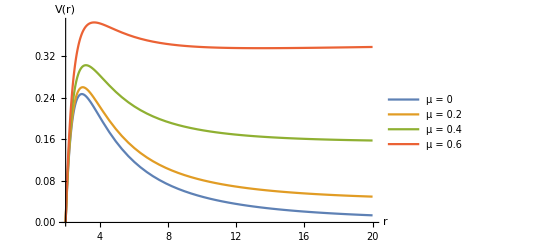

```mathematica
Plot[Evaluate@Table[Vtemp/.mphi->m,{m,{0,0.2,0.4,0.6}}],{r,2.001,20},PlotLegends->{"μ = 0","μ = 0.2","μ = 0.4","μ = 0.6"},AxesLabel->{"r","V(r)"},PlotRange->All]
```